## 多线程运行

注： 命令行输入 top 查看 CPU 占用情况

### 测试阶段

#### 函数-Parallelize

并行运算，自动化进行

```mathematica
f1[n_]:=Length[FactorInteger[(10^n-1)/9]];
f1/@Range[70]//Last//Timing
```

{4.54149,12}

```mathematica
Parallelize[Map[f1,Range[70]]]//Last//Timing
```

{0.185287,12}

```mathematica
$KernelCount
```

4

#### 函数-ParallelTry

并行运算，其中一个得到结果时停止

```mathematica
ClearAll[f];
f[x_]:=(Pause[RandomInteger[{1,100}]/20];
Print[x,"\t",$KernelCount];
Pause[RandomInteger[{20}]];
Print[x+10,"\t",$KernelCount];
x+20);
```

```mathematica
ParallelTry[f,Range@10]
```

1	4

2	4

3	4

4	4

14	4

24

#### 内核

```mathematica
$KernelCount
```

```mathematica
(*新增内核*)
LaunchKernels[10];
```

```mathematica
(*关闭内核*)
CloseKernels[];
```

#### 函数-ParallelMap

```mathematica
LaunchKernels[10];
```

```mathematica
ParallelMap[f,Range@20]
```

#### 临界区（全局解释器锁）

相关函数

```mathematica
SetSharedVariable
DistributeDefinitions
CriticalSection
```

```mathematica
(*没有设置锁*)
SetSharedVariable[xs];
xs=0;
ParallelDo[xs=xs+1,{10}];
xs
```

4

```mathematica
(*设置锁*)
SetSharedVariable[xs];
xs=0;
ParallelDo[CriticalSection[a,xs=xs+1],{10}];
xs
```

10

#### 测试全局锁

```mathematica
CloseKernels[];
LaunchKernels[5];
```

单个锁

```mathematica
ClearAll[f,lock];
SetSharedVariable[var];
var=0;
f[x_]:=(Pause[RandomInteger[{1,100}]/20];
Print[x,"\t",$KernelCount];
Pause[RandomInteger[{20}]/20];
Print[x+10,"\t",$KernelCount];
CriticalSection[lock,Print["here I lock something\t",var=var+1];];
x+20);
ParallelMap[f,Range@8]
```

两个锁

```mathematica
ClearAll[f,lock1,lock2];
f[n_]:=If[n==1||n==4,CriticalSection[lock1,Print["lock 1\t",n];Pause[5]],CriticalSection[lock2,Print["lock 2\t",n];Pause[1]]];
```

```mathematica
ParallelMap[f,Range@8]
```

lock 1	1

lock 2	3

lock 2	5

lock 2	6

lock 2	7

lock 2	8

lock 1	4

lock 2	2

{Null,Null,Null,Null,Null,Null,Null,Null}

### 准备函数

#### 内容汇总

——基础函数——
GraphF[k_?Positive]
	构造特殊子图 F_k
GraphK3[k_?Positive]
	K3 的若干 copies
SubGraph
	判别是否为子图
ExtremalGraphs[graphs_,forbidden_,edge_:0]
	从给定图中筛选子图

——简单图相关数据——
第八阶 12 346
第九阶 274 668
第十阶 12 005 168
第十一阶 1 018 997 864

——文件分割——
第九阶 8
第十阶 391
第十一阶 -

#### 导入函数

```mathematica
SetDirectory[NotebookDirectory[]]
<<extremal.m;
?Extremal`*
```

/home/rex/desktop/work_space/1 MMA/4 ExtremalGraphs

Loading functions about extremal graphs...

#### 获取部分简单图

```mathematica
SimpleGraphs[n_,a_,b_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph"<>ToString@n<>".g6",{"GraphList",Range[a,b]}];
```

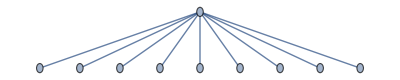
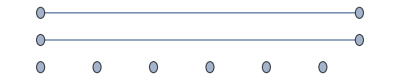
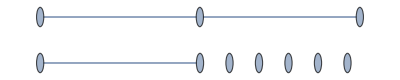
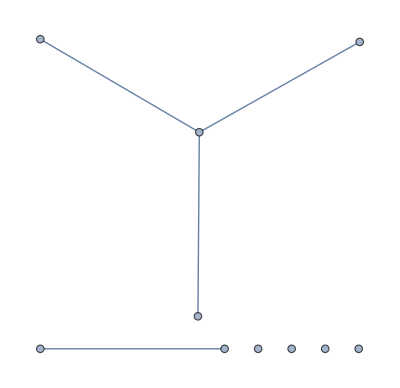
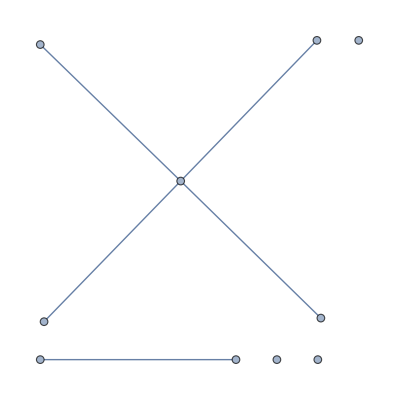
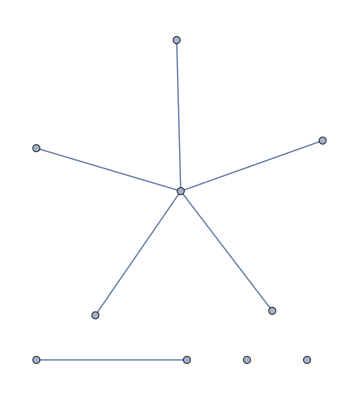

```mathematica
SimpleGraphs[10,10,15]
```

```mathematica
path="~/desktop/work_space/1 MMA/0 pkg/simplegraphs";
SimpleGraphs[n_,k_]:=Import[ToString@StringForm["`1`/graph`2`/graph`2`-`3`.g6",path,n,k]];
```

```mathematica
graphs=SimpleGraphs[9,1];
```

#### 多线程拆分

```mathematica
SetDirectory[NotebookDirectory[]];
ParallelNeeds["Extremal`"];
```

```mathematica
LaunchKernels[50];
$KernelCount
```

150

```mathematica
ClearAll[lock];
SetSharedVariable[size,step,n,medge,graphs,forbidden];
Needs["Extremal`"]
(*size of simple graphs of n vertices*)
forbidden=GraphF[2];
{n,size}={9,274668};
(*{n,size}={8,12346};*)
step=10^3;
(*output results*)
medge=0;
graphs={};
```

```mathematica
ChkPart[k_]:=Module[{edge=medge,newgraphs,a,b},
{a,b}={(k-1) step+1,k step};
If[a>size,Return[Nothing]];
If[b>size,b=size];
{newgraphs,edge}=ExtremalGraphs[SimpleGraphs[n,a,b],forbidden,edge];
CriticalSection[lock,Which[
edge<medge,Return[Nothing],
edge>medge,medge=edge;graphs=newgraphs,
edge==medge,medge=edge;graphs=Join[graphs,newgraphs]]];Nothing]
```

### 调试使用

#### 公共内容

```mathematica
SetDirectory[NotebookDirectory[]];
ParallelNeeds["Extremal`"];
Needs["Extremal`"]
```

Loading functions about extremal graphs...

```mathematica
ClearAll[lock];
SetSharedVariable[size,medge,graphs,forbidden];
forbidden=GraphF[2];
```

```mathematica
ChkPart[n_][k_]:=ChkPart[n,k];
ChkPart[n_,k_]:=Module[{edge,newgraphs},
{newgraphs,edge}=ExtremalGraphs[SimpleGraphs[n,k],forbidden,medge];
CriticalSection[lock,Which[
edge<medge,Null,
edge>medge,medge=edge;graphs=newgraphs,
edge==medge,graphs=Join[graphs,newgraphs]];
Print["Checked:\t",n,"\t",k,
"\tedge:",edge,"\nnewgraphs:",Length@newgraphs,
"\tmedge:",medge,"\textremal graphs:",Length@graphs]];Nothing]
```

#### 第九阶

```mathematica
{n,size}={9,8};
CloseKernels[];
LaunchKernels[7];
$KernelCount
```

```mathematica
medge=0;graphs={};
ParallelMap[ChkPart[n],Range@size]//Timing
```

Checked:	9	8
newgraphs:0	medge:0	extremal graphs:0

Checked:	9	1
newgraphs:1	medge:21	extremal graphs:1

Checked:	9	5
newgraphs:1	medge:21	extremal graphs:2

Checked:	9	3
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	6
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	4
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	7
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	2
newgraphs:0	medge:21	extremal graphs:2

{1.68937,{}}

#### 第十阶

51 线程用时 488s
101 线程用时 278 - 290s

```mathematica
{n,size}={10,391};
CloseKernels[];
LaunchKernels[100];
$KernelCount
```

100

```mathematica
medge=0;graphs={};
ParallelMap[ChkPart[n],Range[Min[9,size]]]//Timing
ParallelMap[ChkPart[n],Range[10,size]]//Timing
```

{20.815,{}}

Checked:	10	373	edge:26
newgraphs:0	medge:26	extremal graphs:1

Checked:	10	353	edge:26
newgraphs:0	medge:26	extremal graphs:1

Checked:	10	351	edge:26
newgraphs:0	medge:26	extremal graphs:1

Checked:	10	355	edge:26
newgraphs:0	medge:26	extremal graphs:1

Checked:	10	349	edge:26
newgraphs:0	medge:26	extremal graphs:1

{269.221,{}}

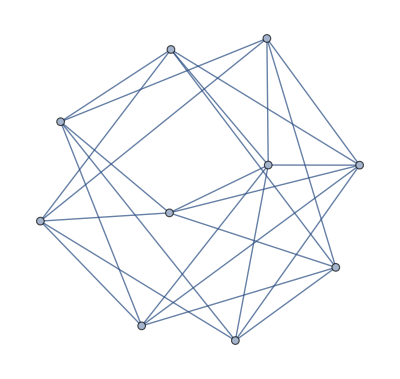

```mathematica
graphs
```